```mathematica
<<MaTeX`
```

```mathematica
Import["/Users/miguelangel/elipse.txt","Table"]
```

{{1.,0.},{1.0002,0.001},{1.0004,0.002},{1.0006,0.003},{1.00079,0.00399999},{1.00099,0.00499998},19990,{0.99027,-0.0438125},{0.990513,-0.0428144},{0.990756,-0.0418158},{0.990997,-0.0408168},{0.991238,-0.0398174}}
 |  |  |  |

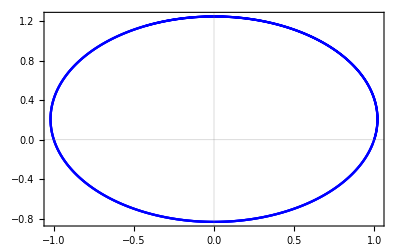

```mathematica
a=ListLinePlot[%2,PlotTheme->"Scientific",PlotStyle->Blue,FrameLabel->MaTeX@{HoldForm[x],HoldForm[y]}]
```

```mathematica
Import["/Users/miguelangel/polares.txt","Table"]
```

{{0.,1.},{0.0009998,1.0002},{0.0019992,1.0004},{0.0029982,1.0006},{0.0039968,1.0008},{0.004995,1.001},19990,{18.8053,0.991238},{18.8064,0.991438},{18.8074,0.991638},{18.8084,0.991838},{18.8094,0.992038}}
 |  |  |  |

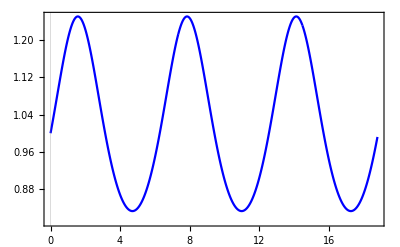

```mathematica
b=ListLinePlot[%4,PlotTheme->"Scientific",PlotStyle->Blue,FrameLabel->MaTeX@{HoldForm[θ],HoldForm[r]}]
```

```mathematica
Import["/Users/miguelangel/r(t).txt","Table"]
```

{{0.,1.},{0.001,1.0002},{0.002,1.0004},{0.003,1.0006},{0.004,1.0008},{0.005,1.001},19990,{19.9966,0.991238},{19.9976,0.991438},{19.9986,0.991638},{19.9996,0.991838},{20.0006,0.992038}}
 |  |  |  |

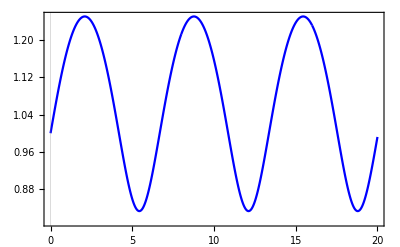

```mathematica
c=ListLinePlot[%7,PlotTheme->"Scientific",PlotStyle->Blue,FrameLabel->MaTeX@{HoldForm[t],HoldForm[r]}]
```

```mathematica
Import["/Users/miguelangel/theta(t).txt","Table"]
```

{{0.,0.},{0.001,0.0009998},{0.002,0.0019992},{0.003,0.0029982},{0.004,0.0039968},{0.005,0.004995},19990,{19.9966,18.8053},{19.9976,18.8064},{19.9986,18.8074},{19.9996,18.8084},{20.0006,18.8094}}
 |  |  |  |

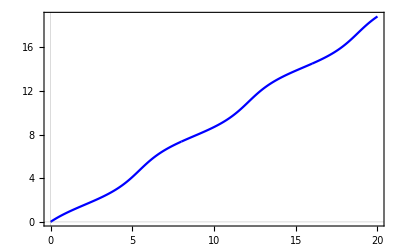

```mathematica
d=ListLinePlot[%10,PlotTheme->"Scientific",PlotStyle->Blue,FrameLabel->MaTeX@{HoldForm[t],HoldForm[θ]}]
```

```mathematica
Import["/Users/miguelangel/rp(t).txt","Table"]
```

{{0.,0.2},{0.001,0.2},{0.002,0.2},{0.003,0.199999},{0.004,0.199998},{0.005,0.199998},19990,{19.9966,0.199799},{19.9976,0.199808},{19.9986,0.199817},{19.9996,0.199825},{20.0006,0.199833}}
 |  |  |  |

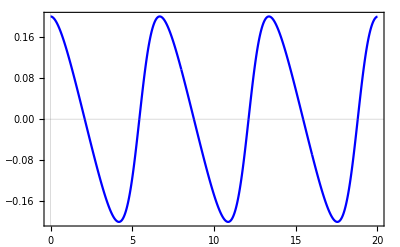

```mathematica
e=ListLinePlot[%12,PlotTheme->"Scientific",PlotStyle->Blue,FrameLabel->MaTeX@{HoldForm[t],HoldForm[Subscript[r,p]]}]
```

```mathematica
Export["trayectoria.png",a]
```

trayectoria.png

```mathematica
Export["rvstheta.png",b]
```

rvstheta.png

```mathematica
Export["rvst.png",c]
```

rvst.png

```mathematica
Export["thetavst.png",d]
```

thetavst.png

```mathematica
Export["rpvst.png",e]
```

rpvst.png